```mathematica
Q:=1.293
H:=1.13
tau:=886.7
lambda[x_]:=(255/(tau*x^5))*(12+6*x+x^2)
t[T_]:=132*(0.1/T)^2
```

```mathematica
s=NDSolve[{Y'[x]==x*lambda[x]*(Exp[-x]-Y[x]*(1+Exp[-x]))/H,Y[Q/0.07]==0.11},Y[x],{x,Q/1.1, Q/0.05}]
```

{{Y[x]→InterpolatingFunction[{{1.17545,25.86}},<>][x]}}

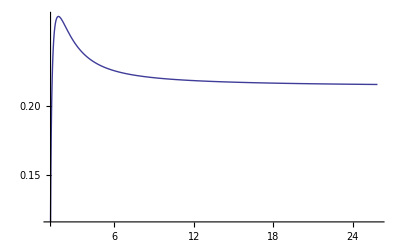

```mathematica
LogPlot[Evaluate[2*Y[x]/.s],{x,Q/1.1, Q/0.05},PlotRange->All]
```

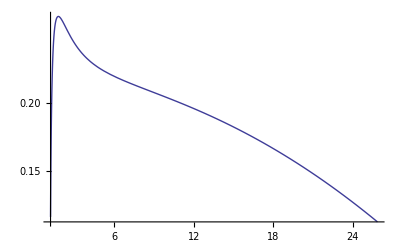

```mathematica
LogPlot[Evaluate[2*Y[x]*Exp[-t[Q/x]/tau]/.s],{x,Q/1.1, Q/0.05},PlotRange->All]
```